```mathematica
getallmutations[{n_Integer, k_Integer, r_Integer}] := 
 Module[{digits = List/@IntegerDigits[n, k, k^(2r+1)], mudigs},
mudigs =(Tuples[ReplacePart[digits, #->Complement[Range[0, k - 1], digits[[#]]]]]&/@ Range[Length[digits]-1] )// Flatten[#, 1]&;
{#, k, r}&/@ (FromDigits[#, k]&/@ mudigs)
  ]
```

### Sequential rule

#### All single-cell perturbation distribution

```mathematica
Module[{rule = {240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1}, aps},aps = {{"[◼]", "allperts"}}[First[[rule, {Join[Table[1,5],{2}],0},{100,{-100, 100}}, <||>]], 6];outputs = If[Length[#]===0,0,Last[#]-First[#]+1]&[{{"[◼]", "nonzeroRange"}}[#]]&[First[[rule, {Join[Table[1,5],{2}],0},{{{100}},{-100, 100}}, #]]]&/@ aps];
```

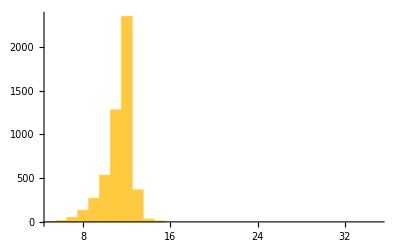

```mathematica
Histogram[outputs, {1}, PlotRange->{{5, 35}, Automatic}]
```

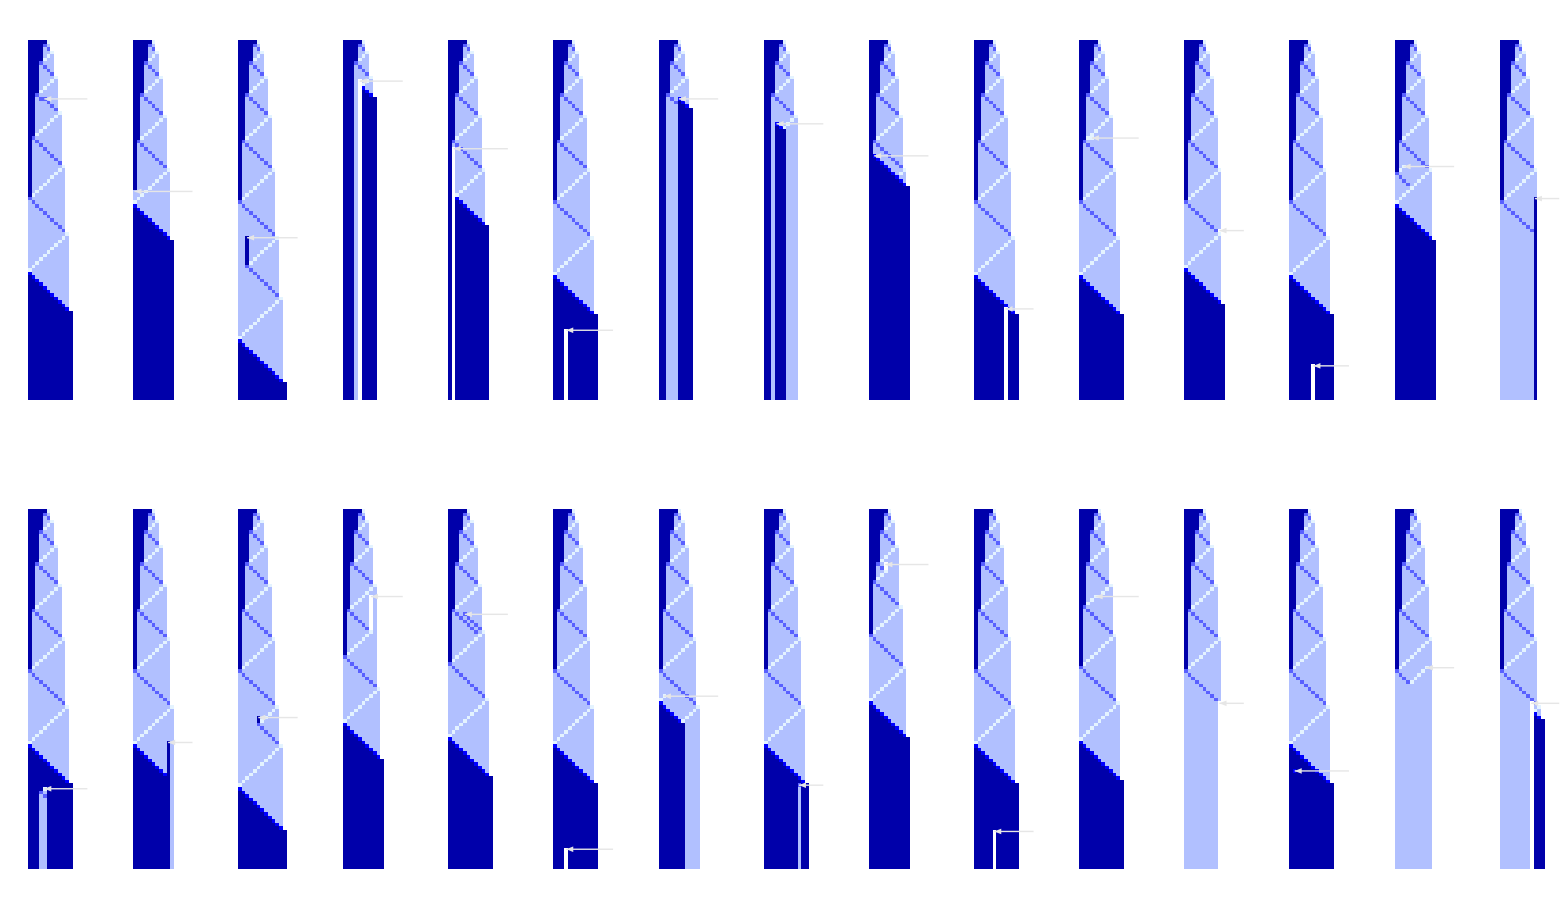

```mathematica
GraphicsGrid[Partition[Module[{rule = {240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1}},Table[SeedRandom[444332 +i];
{{"[◼]", "PerturbedArrayPlot"}}[#1, If[#2 == <||>, {}, First[Keys[#2]]], ColorRules->Join[{0->White, 1->Darker[Blue]},Table[ i->Blend[{White, LightBlue, Blue}, i/5], {i, 2, 5}]], Mesh->False, "ArrowStyle"->Directive[Arrowheads[Medium],GrayLevel[.9], Haloing[Red, 1]],"ArrowDirection"->Left,"InitialIndex"->0]&@@[rule, {Join[Table[1,5],{2}],0},{100,{-5, 15}}], {i, 30}]], 15]]
```

#### two perturbations

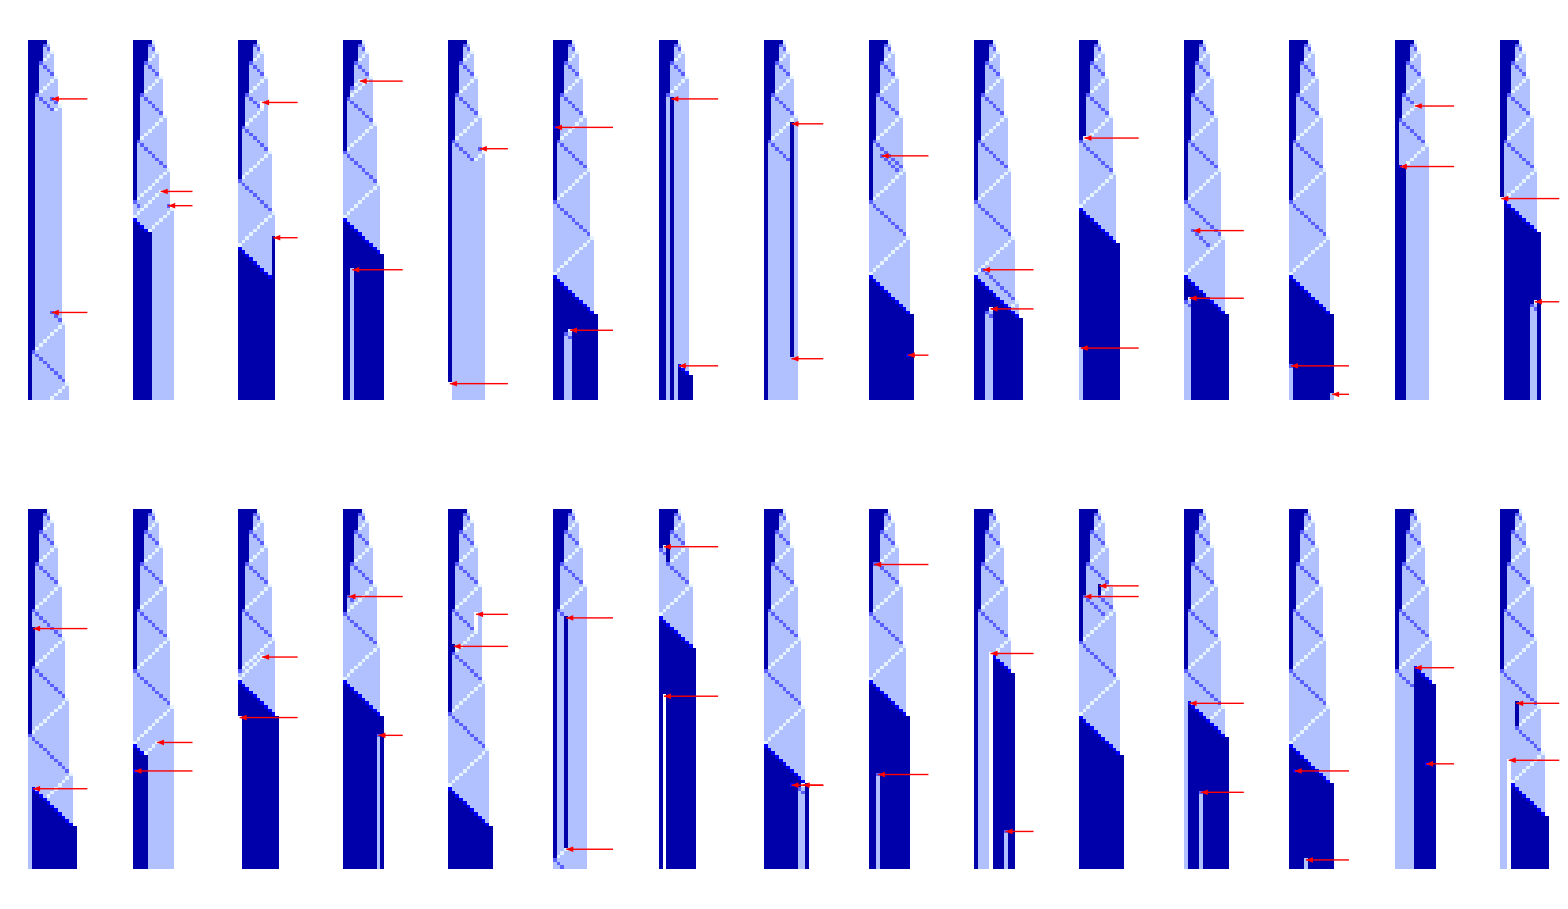

```mathematica
GraphicsGrid[Partition[Module[{rule = {240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1}},Table[SeedRandom[444332 +i];
{{"[◼]", "PerturbedArrayPlot"}}[#1, If[#2 == <||>, {}, Keys[#2]], ColorRules->Join[{0->White, 1->Darker[Blue]},Table[ i->Blend[{White, LightBlue, Blue}, i/5], {i, 2, 5}]], Mesh->False, "ArrowStyle"->Directive[Arrowheads[Medium],GrayLevel[.9], Haloing[Red, 1]],"ArrowDirection"->Left,"InitialIndex"->0]&@@[rule, {Join[Table[1,5],{2}],0},{100,{-5, 15}}, 2], {i, 30}]], 15]]
```

#### Single rule perturbation distribution

```mathematica
Module[{rule = {240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1}},outsrule = If[Length[#]===0,0,Last[#]-First[#]+1]&[{{"[◼]", "nonzeroRange"}}[#]]&[CellularAutomaton[#, {Join[Table[1,5],{2}],0},{{{100}},{-100, 100}}]]&/@ getallmutations[rule]];
```

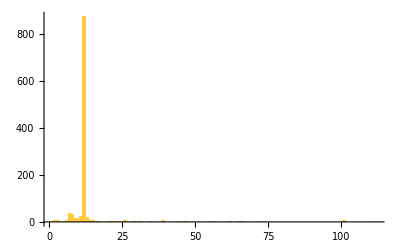

```mathematica
Histogram[outsrule, {1}]
```

```mathematica
Module[{rule = {240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1}},
Length[getallmutations[rule]]]
```

1075

#### Multiple rule perturbation distribution

Dual

```mathematica
Module[{rule = {240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1}},
omr = Table[
SeedRandom[444444 + i];If[Length[#]===0,0,Last[#]-First[#]+1]&[{{"[◼]", "nonzeroRange"}}[#]]&[CellularAutomaton[{{"[◼]", "RandomRuleMutation"}}[rule, 2], {Join[Table[1,5],{2}],0},{{{100}},{-100, 100}}]], {i, 2000}]];
```

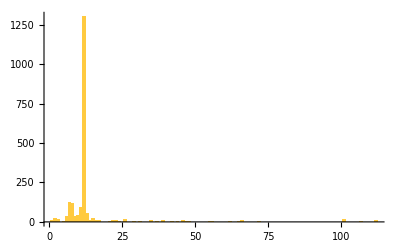

```mathematica
Histogram[omr, {1}, PlotRange->All]
```

Three

```mathematica
Module[{rule = {240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1}},
omr2 = Table[
SeedRandom[444444 + i];If[Length[#]===0,0,Last[#]-First[#]+1]&[{{"[◼]", "nonzeroRange"}}[#]]&[CellularAutomaton[{{"[◼]", "RandomRuleMutation"}}[rule, 3], {Join[Table[1,5],{2}],0},{{{100}},{-100, 100}}]], {i, 2000}]];
```

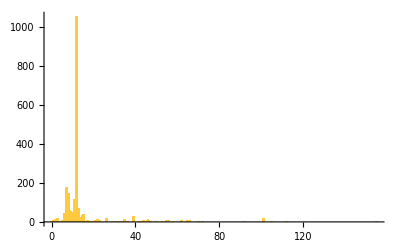

```mathematica
Histogram[omr2, {1}, PlotRange->All]
```

Five

```mathematica
Module[{rule = {240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1}},
omr3 = Table[
SeedRandom[444444 + i];If[Length[#]===0,0,Last[#]-First[#]+1]&[{{"[◼]", "nonzeroRange"}}[#]]&[CellularAutomaton[{{"[◼]", "RandomRuleMutation"}}[rule, 5], {Join[Table[1,5],{2}],0},{{{100}},{-100, 100}}]], {i, 2000}]];
```

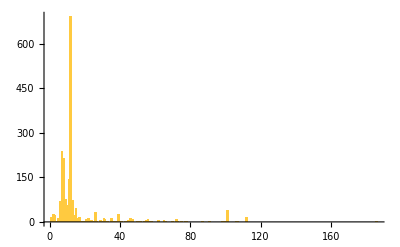

```mathematica
Histogram[omr3, {1}, PlotRange->All]
```

Ten

```mathematica
Module[{rule = {240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1}},
omr4= Table[
SeedRandom[444444 + i];If[Length[#]===0,0,Last[#]-First[#]+1]&[{{"[◼]", "nonzeroRange"}}[#]]&[CellularAutomaton[{{"[◼]", "RandomRuleMutation"}}[rule, 10], {Join[Table[1,5],{2}],0},{{{100}},{-100, 100}}]], {i, 2000}]];
```

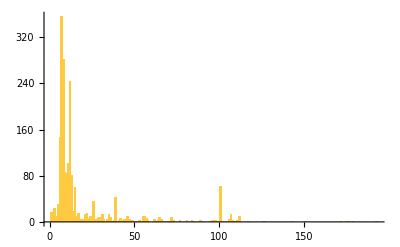

```mathematica
Histogram[omr4, {1}, PlotRange->All]
```

Twenty

```mathematica
Module[{rule = {240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1}},
omr5= Table[
SeedRandom[444444 + i];If[Length[#]===0,0,Last[#]-First[#]+1]&[{{"[◼]", "nonzeroRange"}}[#]]&[CellularAutomaton[{{"[◼]", "RandomRuleMutation"}}[rule, 20], {Join[Table[1,5],{2}],0},{{{100}},{-100, 100}}]], {i, 2000}]];
```

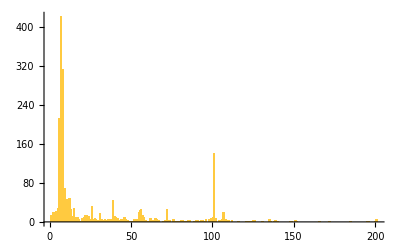

```mathematica
Histogram[omr5, {1}, PlotRange->All]
```

#### Shuffling ruleset instead of poking it

#### Sequential feature space plot

```mathematica
SeedRandom[443568];Magnify[FeatureSpacePlot[Rasterize[#]->#&/@Module[{rule = {240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1}, aps},aps = {{"[◼]", "allperts"}}[First[[rule, {Join[Table[1,5],{2}],0},{100,{-100, 100}}, <||>]], 6];(ArrayPlot[ArrayPad[#, 1]&/@ResourceFunction["ArrayCrop"][#], ColorRules->Join[{0->White, 1->Darker[Blue]},Table[ i->Blend[{White, LightBlue, Blue}, i/5], {i, 2, 5}]], Mesh->False]&@@[rule, {Join[Table[1,5],{2}],0},{100,{-100, 100}}, #]&)/@ RandomSample[aps, 400]], LabelingSize->100,PlotStyle->AbsolutePointSize[9],Frame->True,FrameTicks->None,FrameStyle->Gray,RandomSeeding->64453,PerformanceGoal->"Static",ImageSize->2000], .31]
```

-Graphics-

### Parallel Rule

#### Parallel outcomes

```mathematica
Module[{rule = {837428508144, 3, 1}, aps},aps = {{"[◼]", "allperts"}}[First[[rule, {Join[Table[1,5],{2}],0},{100,{-100, 100}}, <||>]], 3];outputs2 = If[Length[#]===0,0,Last[#]-First[#]+1]&[{{"[◼]", "nonzeroRange"}}[#]]&[First[[rule, {Join[Table[1,5],{2}],0},{{{100}},{-100, 100}}, #]]]&/@ aps];
```

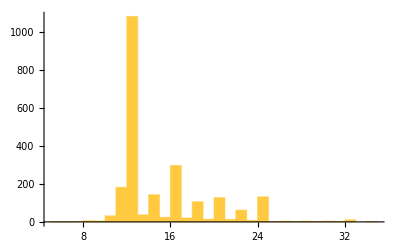

```mathematica
Histogram[outputs2, PlotRange->All]
```

#### Parallel Feature Space Plot

```mathematica
SeedRandom[443568];Magnify[FeatureSpacePlot[Rasterize[#]->#&/@Module[{rule = {837428508144, 3, 1}, aps},aps = {{"[◼]", "allperts"}}[First[[rule, {Join[Table[1,5],{2}],0},{100,{-100, 100}}, <||>]], 3];(ArrayPlot[ArrayPad[#, 1]&/@ResourceFunction["ArrayCrop"][#], ColorRules->Join[{0->White, 1->Darker[Blue]},Table[ i->Blend[{White, LightBlue, Blue}, i/5], {i, 2, 5}]], Mesh->False]&@@[rule, {Join[Table[1,5],{2}],0},{100,{-100, 100}}, #]&)/@ RandomSample[aps, 400]], LabelingSize->100,PlotStyle->AbsolutePointSize[9],Frame->True,FrameTicks->None,FrameStyle->Gray,RandomSeeding->64453,PerformanceGoal->"Static",ImageSize->2000], .31]
```

-Graphics-

#### Rule perturbation distribution

```mathematica
Module[{rule = {837428508144, 3, 1}},outsrule2 = If[Length[#]===0,0,Last[#]-First[#]+1]&[{{"[◼]", "nonzeroRange"}}[#]]&[CellularAutomaton[#, {Join[Table[1,5],{2}],0},{{{100}},{-100, 100}}]]&/@ getallmutations[rule]];
```

```mathematica
Module[{rule = {837428508144, 3, 1}},outsrule2 = If[Length[#]===0,0,Last[#]-First[#]+1]&[{{"[◼]", "nonzeroRange"}}[#]]&[CellularAutomaton[#, {Join[Table[1,5],{2}],0},{{{100}},{-100, 100}}]]&/@ VertexList[NestGraph[getallmutations,{rule},2]]];
```

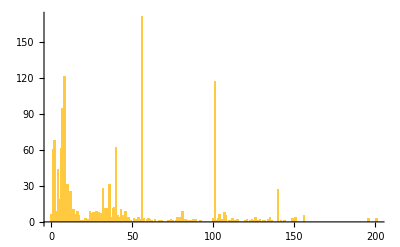

```mathematica
Histogram[outsrule2, {1}]
```